```mathematica
(*f=Subscript[a, 6]*t^6+Subscript[a, 5]*t^5+Subscript[a, 4]*t^4+Subscript[a, 3]*t^3+Subscript[a, 2]*t^2+Subscript[a, 1]*t+Subscript[a, 0];*)
f=Subscript[a, 5]*t^5+Subscript[a, 4]*t^4+Subscript[a, 3]*t^3+Subscript[a, 2]*t^2+Subscript[a, 1]*t+Subscript[a, 0];
```

```mathematica
eqn1=x0-f==0/.t->t0
```

x0-a_0-t0 a_1-t0^2 a_2-t0^3 a_3-t0^4 a_4-t0^5 a_5==0

```mathematica
eqn2=xdot0-D[f,t]==0/.t->t0
```

xdot0-a_1-2 t0 a_2-3 t0^2 a_3-4 t0^3 a_4-5 t0^4 a_5==0

```mathematica
eqn3=xddot0-D[D[f,t],t]==0/.t->t0
```

xddot0-2 a_2-6 t0 a_3-12 t0^2 a_4-20 t0^3 a_5==0

```mathematica
eqn4=xf-f==0/.t->tf
```

xf-a_0-tf a_1-tf^2 a_2-tf^3 a_3-tf^4 a_4-tf^5 a_5==0

```mathematica
eqn5=0-D[f,t]==0/.t->tf
```

-a_1-2 tf a_2-3 tf^2 a_3-4 tf^3 a_4-5 tf^4 a_5==0

```mathematica
eqn6=0-D[D[f,t],t]==0/.t->tf
```

-2 a_2-6 tf a_3-12 tf^2 a_4-20 tf^3 a_5==0

```mathematica
eqnSubs=Solve[eqn1&&eqn2&&eqn3&&eqn4&&eqn5&&eqn6,{Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[a, 5]}]⟦1⟧//FullSimplify
```

{a_0→(tf^3 (-2 tf^2 x0-t0^4 xddot0+2 t0^3 (tf xddot0+4 xdot0)+2 t0 tf (5 x0+tf xdot0)-t0^2 (20 x0+tf (tf xddot0+10 xdot0)))+2 t0^3 (t0^2-5 t0 tf+10 tf^2) xf)/(2 (t0-tf)^5),a_1→(tf^2 (3 t0^4 xddot0-2 tf^3 xdot0+2 t0 tf^2 (tf xddot0+5 xdot0)-4 t0^3 (tf xddot0+6 xdot0)+t0^2 (60 x0-tf^2 xddot0+16 tf xdot0-60 xf)))/(2 (t0-tf)^5),a_2→-(tf (3 t0^4 xddot0+tf^4 xddot0-24 t0^3 xdot0+4 t0^2 (15 x0-2 tf^2 xddot0-3 tf xdot0-15 xf)+4 t0 tf (15 x0+tf^2 xddot0+9 tf xdot0-15 xf)))/(2 (t0-tf)^5),a_3→(t0^4 xddot0+4 t0^3 (tf xddot0-2 xdot0)+4 t0 tf (20 x0+7 tf xdot0-20 xf)+tf^2 (20 x0+3 tf (tf xddot0+4 xdot0)-20 xf)-4 t0^2 (-5 x0+2 tf^2 xddot0+8 tf xdot0+5 xf))/(2 (t0-tf)^5),a_4→(-2 t0^3 xddot0+t0^2 (tf xddot0+14 xdot0)-tf (30 x0+3 tf^2 xddot0+16 tf xdot0-30 xf)+t0 (-30 x0+2 tf (2 tf xddot0+xdot0)+30 xf))/(2 (t0-tf)^5),a_5→(12 x0+(t0-tf) (t0 xddot0-tf xddot0-6 xdot0)-12 xf)/(2 (t0-tf)^5)}

```mathematica
f/.eqnSubs//FullSimplify
```

1/(2 (t0-tf)^5)(tf^3 (-2 tf^2 x0-t0^4 xddot0+2 t0^3 (tf xddot0+4 xdot0)+2 t0 tf (5 x0+tf xdot0)-t0^2 (20 x0+tf^2 xddot0+10 tf xdot0))+t tf^2 (3 t0^4 xddot0-2 tf^3 xdot0+2 t0 tf^2 (tf xddot0+5 xdot0)-4 t0^3 (tf xddot0+6 xdot0)+t0^2 (60 x0-tf^2 xddot0+16 tf xdot0-60 xf))-t^2 tf (3 t0^4 xddot0+tf^4 xddot0-24 t0^3 xdot0+4 t0^2 (15 x0-2 tf^2 xddot0-3 tf xdot0-15 xf)+4 t0 tf (15 x0+tf^2 xddot0+9 tf xdot0-15 xf))+t^5 (12 x0+(t0-tf) (t0 xddot0-tf xddot0-6 xdot0)-12 xf)+2 t0^3 (t0^2-5 t0 tf+10 tf^2) xf+t^3 (t0^4 xddot0+4 t0^3 (tf xddot0-2 xdot0)+4 t0 tf (20 x0+7 tf xdot0-20 xf)+tf^2 (20 x0+3 tf (tf xddot0+4 xdot0)-20 xf)-4 t0^2 (-5 x0+2 tf^2 xddot0+8 tf xdot0+5 xf))+t^4 (-2 t0^3 xddot0+t0^2 (tf xddot0+14 xdot0)-tf (30 x0+3 tf^2 xddot0+16 tf xdot0-30 xf)+t0 (-30 x0+2 tf (2 tf xddot0+xdot0)+30 xf)))

```mathematica
D[f,t]/.eqnSubs//FullSimplify
```

1/(2 (t0-tf)^5)(t-tf)^2 (3 t0^4 xddot0-2 tf^3 xdot0+2 t0 tf^2 (tf xddot0+5 xdot0)-4 t0^3 (tf xddot0+6 xdot0)-2 t (4 t0^3 xddot0+tf^2 (tf xddot0+2 xdot0)-7 t0^2 (tf xddot0+4 xdot0)+2 t0 (30 x0+tf^2 xddot0+13 tf xdot0-30 xf))+t0^2 (60 x0-tf^2 xddot0+16 tf xdot0-60 xf)+5 t^2 (12 x0+(t0-tf) (t0 xddot0-tf xddot0-6 xdot0)-12 xf))

```mathematica
D[D[f,t],t]/.eqnSubs//FullSimplify
```

1/(t0-tf)^5(t-tf) (3 t0^4 xddot0+tf^4 xddot0-24 t0^3 xdot0+4 t0^2 (15 x0-2 tf^2 xddot0-3 tf xdot0-15 xf)+4 t0 tf (15 x0+tf^2 xddot0+9 tf xdot0-15 xf)+10 t^2 (12 x0+(t0-tf) (t0 xddot0-tf xddot0-6 xdot0)-12 xf)+4 t (-3 t0^3 xddot0+t0^2 (4 tf xddot0+21 xdot0)-tf (15 x0+2 tf^2 xddot0+9 tf xdot0-15 xf)+t0 (-45 x0+tf^2 xddot0-12 tf xdot0+45 xf)))

```mathematica
x0=0.2;
xdot0=0.1;
xddot0=0.01;
xf=1;
t0 = 0.2;
tf = 1.2;
```

```mathematica
f/.eqnSubs/.t->0.2
```

0.2

```mathematica
Subscript[a, 2]/.eqnSubs
```

-7.47

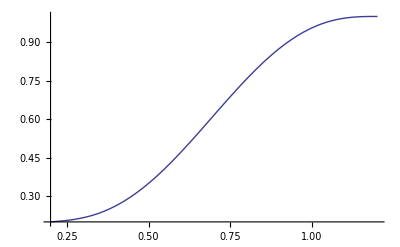

```mathematica
Plot[f/.eqnSubs,{t,t0,tf}]
```